```mathematica
Quit[];
```

```mathematica
1;
```

```mathematica
(*
The definition of Deposit and BankPayoff:

   I changed the original version of the code so that it can solve the equation
  first, use NIntegrate. then we need ensure every element in the integration is
  numbers, so put values1 into the equation everytime the function calls.

 second, use numberQ to ensure the number elment.
*)
Values1={V->2,α->.1,β->1,y->.01,δ->10};
Deposit[ψ_,R_,Values1_]:=1-CDF[NormalDistribution[0,1],α/(√β) (ψ-y+R (√(α+β))/α)+√β (ψ-θ)]/.Values1;
BankPayoff[ψ_?NumberQ,R_?NumberQ,Values1_]:=((V-1/CDF[NormalDistribution[0,1],R]) /.Values1)NIntegrate[Deposit[ψ,R,Values1] PDF[NormalDistribution[y,√(1/α)]/.Values1,θ],{θ,ψ,+∞}];
```

```mathematica
(*
for every R, we find the argmax of BankPayoff based on the root of ψ equation
There are some warnings in the codes, but they do not matter, the NArgmax have two 
 reserved way to calculate. So you can see the precision of the result is higher than R. But it is the accurate result
*)
NArgMax[{
ψtemp=ψ/.FindRoot[ψ==((δ CDF[NormalDistribution[0,1],(α/(√β) (ψ-y+R (√(α+β))/α))/.Values1])/.Values1),{ψ,10}];
BankPayoff[ψtemp,R,Values1]
},{R,0.01,10}]
```

FindRoot::nlnum: The function value {10.-5. Erfc[-0.0707107 (9.99+10.4881 R)]} is not a list of numbers with dimensions {1} at {ψ} = {10.}.

ReplaceAll::reps: {FindRoot[ψ==(δ CDF[NormalDistribution[0,1],Times[«2»]/.Values1]/.Values1),{ψ,10}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {10.-5. Erfc[-0.0707107 (9.99+10.4881 R)]} is not a list of numbers with dimensions {1} at {ψ} = {10.}.

ReplaceAll::reps: {FindRoot[ψ==(δ CDF[NormalDistribution[0,1],Times[«2»]/.Values1]/.Values1),{ψ,10}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {10.-5. Erfc[-0.0707107 (9.99+10.4881 R)]} is not a list of numbers with dimensions {1} at {ψ} = {10.}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[ψ==(δ CDF[NormalDistribution[0,1],Times[«2»]/.Values1]/.Values1),{ψ,10}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

0.213184

```mathematica
(*
If you do not trust the Nargmax, you can use my own function to find the max value in the BankPayOff
*)
indMax[f_,X_,minStep_]:=Module[{min,temp1,temp2,step},step=(X[[3]]-X[[2]])/2;min=X[[2]];
While[2 step>minStep,step=step/10;
temp1=f[min];
While[temp2=f[min=min+step];temp2>temp1,temp1=temp2];
min=min-2 step;];
{X[[1]],min,min+2 step}]
```

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

```mathematica
0.2131842357929021
```

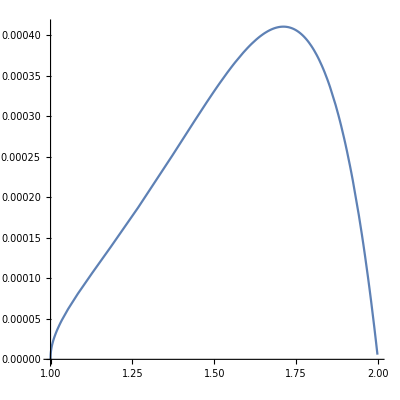

```mathematica
(*
We can plot the Subscript[r, D] and BankPayoff line, the argmax is about 1.71
*)
ParametricPlot[{1/CDF[NormalDistribution[0,1],R],
ψtemp=ψ/.FindRoot[ψ==((δ CDF[NormalDistribution[0,1],(α/(√β) (ψ-y+R (√(α+β))/α))/.Values1])/.Values1),{ψ,10}];
BankPayoff[ψtemp,R,Values1]
},{R,0.001,10},PlotRange->All,AspectRatio->1]
```

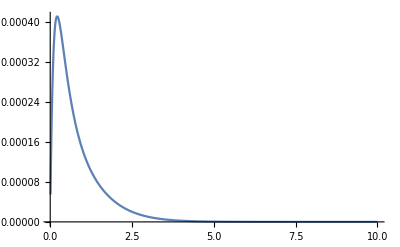

```mathematica
(*The R and BankPayoff result*)
Plot[{
ψtemp=ψ/.FindRoot[ψ==((δ CDF[NormalDistribution[0,1],(α/(√β) (ψ-y+R (√(α+β))/α))/.Values1])/.Values1),{ψ,10}];
BankPayoff[ψtemp,R,Values1]
},{R,0.01,10},PlotRange->All]
```

```mathematica
1;
```

```mathematica
1;
```

```mathematica
(*Inverse solution of Subscript[r, D] = 0.213184 is 1.71*)
1/CDF[NormalDistribution[0,1],R]/.{R-> 0.213184}
```

1.71113

```mathematica
(*
Then we set y from 0.1 to 20, run the loop to get Subscript[r, D] for every y,     the output is a list with y in {y,0.1,20},  and the corresponding Subscript[r, D] It means that for every y,  firstly we find the root of the equation for every R. Then we calulate.for every R, the argmax of BankPayoff.
At last we change y to see the relation between y and Subscript[r, D].

There are some warnings in the NArgmax function, but they do not matter, the NArgmax have two 
 reserved way to calculate. So you can see the precision of the result is higher than R. But it is the accurate result

we can change α β δ in the values1 to change the pattern of the result.
*)
n = 1;ys = Range[200];While[True,
Values1={V->2,α->.1,β->.5,y-> n/10,δ->10};
Deposit[ψ_,R_,Values1_]:=1-CDF[NormalDistribution[0,1],α/(√β) (ψ-y+R (√(α+β))/α)+√β (ψ-θ)]/.Values1;
BankPayoff[ψ_,R_,Values1_]:=((V-1/CDF[NormalDistribution[0,1],R]) /.Values1)NIntegrate[Deposit[ψ,R,Values1] PDF[NormalDistribution[y,√(1/α)]/.Values1,θ],{θ,ψ,+∞}];
Rs =NArgMax[{
ψtemp=ψ/.FindRoot[ψ==((δ CDF[NormalDistribution[0,1],(α/(√β) (ψ-y+R (√(α+β))/α))/.Values1])/.Values1),{ψ,10}];
BankPayoff[ψtemp,R,Values1]
},{R,0.01,10}];
r = 1/CDF[NormalDistribution[0,1],Rs];
ys[[n]] = r;
Print["x:",n/10," ,y:",r];
If[n==200, Break[]];
n++;
]
```

FindRoot::nlnum: The function value {10.-5. Erfc[-0.1 (9.9+7.74597 R)]} is not a list of numbers with dimensions {1} at {ψ} = {10.}.

ReplaceAll::reps: {FindRoot[ψ==(δ CDF[NormalDistribution[0,1],Times[«2»]/.Values1]/.Values1),{ψ,10}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {10.-5. Erfc[-0.1 (9.9+7.74597 R)]} is not a list of numbers with dimensions {1} at {ψ} = {10.}.

ReplaceAll::reps: {FindRoot[ψ==(δ CDF[NormalDistribution[0,1],Times[«2»]/.Values1]/.Values1),{ψ,10}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {10.-5. Erfc[-0.1 (9.9+7.74597 R)]} is not a list of numbers with dimensions {1} at {ψ} = {10.}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[ψ==(δ CDF[NormalDistribution[0,1],Times[«2»]/.Values1]/.Values1),{ψ,10}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NIntegrate::inumr: The integrand 0.126157 ⅇ^(-0.05 (-1/10+θ)^2) (1-1/2 Erfc[(-0.141421 Plus[«3»]-0.707107 Plus[«2»])/(√2)]) has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞,0.+(ψ/.FindRoot[ψ==(Times[«2»]/.Values1),{ψ,10.}])}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

x:1/10 ,y:1.65397

x:1/5 ,y:1.65623

x:3/10 ,y:1.65853

x:2/5 ,y:1.66086

x:1/2 ,y:1.66323

x:3/5 ,y:1.66562

x:7/10 ,y:1.66805

x:4/5 ,y:1.67049

x:9/10 ,y:1.67296

x:1 ,y:1.67545

x:11/10 ,y:1.67795

x:6/5 ,y:1.68046

x:13/10 ,y:1.68298

x:7/5 ,y:1.6855

x:3/2 ,y:1.68802

x:8/5 ,y:1.69053

x:17/10 ,y:1.69303

x:9/5 ,y:1.69552

x:19/10 ,y:1.69798

x:2 ,y:1.70042

x:21/10 ,y:1.70283

x:11/5 ,y:1.7052

$Aborted

```mathematica
(*
Plot the list result.
*)
x=Range[200];
ListLinePlot[Transpose[{x/10,ys[[1;;200]]}],AxesLabel->{"y","r_D"},PlotLabel->Style["r_D~y with {V->2,α->0.1,β→0.5,δ->10}",FontSize->18],Background->LightYellow]
-Graphics-
```

```mathematica
1;
```

```mathematica
(* 
Another version of the process. we directly plot the relation between Subscript[r, D] and y
It uses plot function, runs faster, but we can see no result output.

Reminder: In this way, we need  put y into the funtion
*)
Values1={V->2,α->.1,β->1,δ->10};
Deposit[ψ_,R_,y_,Values1_]:=1-CDF[NormalDistribution[0,1],α/(√β) (ψ-y+R (√(α+β))/α)+√β (ψ-θ)]/.Values1;
BankPayoff[ψ_,R_,y_,Values1_]:=((V-1/CDF[NormalDistribution[0,1],R]) /.Values1)NIntegrate[Deposit[ψ,R,y,Values1] PDF[NormalDistribution[y,√(1/α)]/.Values1,θ],{θ,ψ,+∞}];
```

```mathematica
(*
Directly plot. No loop. Run faster
*)
Plot[{
Rs =R /.NArgMax[{
ψtemp=ψ/.FindRoot[ψ==((δ CDF[NormalDistribution[0,1],(α/(√β) (ψ-y+R (√(α+β))/α))/.Values1])/.Values1),{ψ,10}];
BankPayoff[ψtemp,R,y,Values1]
},{R,0.01,10}];
1/CDF[NormalDistribution[0,1],Rs];
},{y,0.01,10},PlotRange->All,AxesLabel->{"y","r_D"},PlotLabel->Style["r_D~y with {V->2,α->0.1,β→0.5,δ->10}",FontSize->18],Background->LightYellow]
```

$Aborted

```mathematica
(*
The method of changing the α β δ is gridsearch method. first we set a rough grid. α as {0.1,0.5,1},β as {0.1, 0.5, 1}, δ as {10,30,50}. Also the α β δ satisfy δ/Sqrt[2*Pi]*α/Sqrt[β] <`1. the unique 
equilibrium condition.

Then we found that δ can not be too large, α<β<=0.5, so we set α = 0.1 β = 0.5,
and change δ as from 1 to 18. Then we can see the result of the trend of the development of Subscript[r, D] ~ y.

When δ is too large, the nugget of the curve is large so that the start point of Subscript[r, D] is large and approches 2, the upper limit. So there are few space for the curve to change. It comes to a mess. You can see in the picture.
-Graphics-
When the α β δ do not satisfy the unique equilibrium. There will be two solutions,for the equation, so the line split to 2 parts. You can see in the picture.
 -Graphics-

*)
```